```mathematica
SetDirectory@NotebookDirectory[];
assoc=Get["wickSATdata.txt"];
```

```mathematica
assoc // Keys
```

{wrapParams,timeStep,numBools,numParams,threshold,convergeTime,solProbEvo,expectedEnergyEvo,numRecoveries,recoveredIterations,param0Evo,param1Evo,param2Evo,param3Evo,param4Evo,param5Evo,param6Evo,param7Evo,param8Evo,param9Evo,param10Evo,param11Evo,param12Evo,param13Evo,param14Evo,param15Evo,param16Evo,param17Evo,param18Evo,param19Evo,param20Evo,param21Evo,param22Evo,param23Evo}

Vertical gray lines indicate where numerical approximation (e.g. TSVD) was used, since A was not invertible

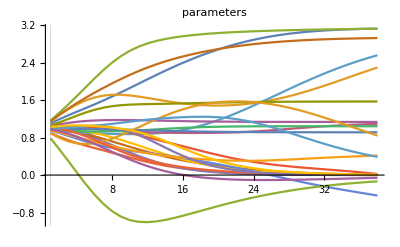

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	%, PlotRange->All, PlotLabel-> "parameters",
	 GridLines -> {assoc["recoveredIterations"], {}}
]
```

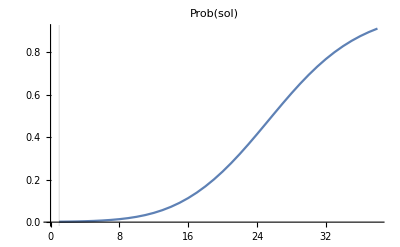

```mathematica
ListLinePlot[
	assoc["solProbEvo"], PlotLabel-> "Prob(sol)",
	GridLines -> {assoc["recoveredIterations"], {}}
]
```

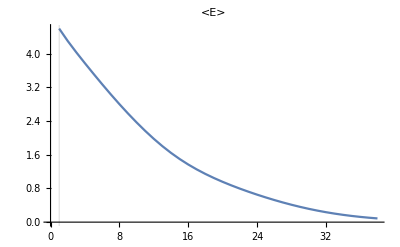

```mathematica
ListLinePlot[
	assoc["expectedEnergyEvo"], PlotLabel -> "<E>",
	GridLines -> {assoc["recoveredIterations"], {}}
]
```